```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=48;
Ly=48;
A=Lx*Ly;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHI[1.0,1.0,1.0,0.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

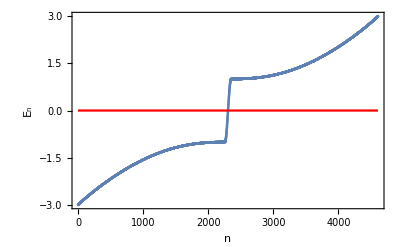

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------- Computation of Bott Index of the whole system -----------------*)
```

```mathematica
(* Clear[vecNormalized,ValVecNor,U,Ux,Vy,U,V,P,LogEigenValuesBott,Bott,BottIndex]  *)
```

```mathematica
(* vecNormalized=Table[Normalize[vec[[i]]],{i,1,2 A}];  *)
```

```mathematica
(* ValVecNor=SortBy[Transpose[{val,vecNormalized}],First]; *)
```

```mathematica
(* FilledEigenvectors=Table[ValVecNor[[i]][[2]], {i,1,A}];  *)
```

```mathematica
(* Clear[P]
P=Table[0,{i,1,2A},{j,1,2A}];  *)
```

```mathematica
(* Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i, 1, A}];  *)
```

```mathematica
(* XList = Flatten[Transpose[Table[i,{i,1,Lx},{j,1,Ly}]]];  *)
```

```mathematica
(* YList = Flatten[Transpose[Table[j,{i,1,Lx},{j,1,Ly}]]];  *)
```

```mathematica
(* XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];  *)
```

```mathematica
(* YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];  *)
```

```mathematica
(* Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];  *)
```

```mathematica
(* Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];  *)
```

```mathematica
(* U = P . Ux. P + IdentityMatrix[2 A] - P;  *)
```

```mathematica
(* V = P . Vy . P + IdentityMatrix[2A] - P;  *)
```

```mathematica
(* Bott = U.V.ConjugateTranspose[U].ConjugateTranspose[V];  *)
```

```mathematica
(* LogEigenValuesBott=Log[Eigenvalues[Bott]];  *)
```

```mathematica
(* BottIndex = Re[(I/(2π))Total[LogEigenValuesBott]]  *)
```

```mathematica
(**----Clear memory for quasicrystal----**)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

4608

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+14
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+6
```

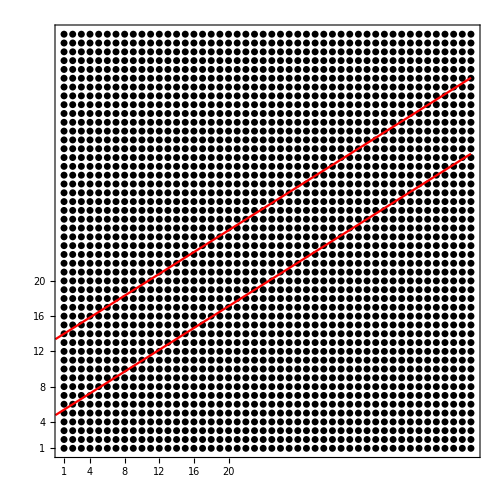

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron,LogEigenValuesBott,Bott, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{241,289,290,291,337,338,339,340,341,385,386,387,388,389,390,433,434,435,436,437,438,439,440,481,482,483,484,485,486,487,488,489,490,529,530,531,532,533,534,535,536,537,538,539,577,578,579,580,581,582,583,584,585,586,587,588,589,626,627,628,629,630,631,632,633,634,635,636,637,638,675,676,677,678,679,680,681,682,683,684,685,686,687,688,725,726,727,728,729,730,731,732,733,734,735,736,737,738,774,775,776,777,778,779,780,781,782,783,784,785,786,787,824,825,826,827,828,829,830,831,832,833,834,835,836,837,874,875,876,877,878,879,880,881,882,883,884,885,886,887,923,924,925,926,927,928,929,930,931,932,933,934,935,936,973,974,975,976,977,978,979,980,981,982,983,984,985,986,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1072,1073,1074,1075,1076,1077,1078,1079,1080,1081,1082,1083,1084,1085,1122,1123,1124,1125,1126,1127,1128,1129,1130,1131,1132,1133,1134,1135,1171,1172,1173,1174,1175,1176,1177,1178,1179,1180,1181,1182,1183,1184,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1271,1272,1273,1274,1275,1276,1277,1278,1279,1280,1281,1282,1283,1320,1321,1322,1323,1324,1325,1326,1327,1328,1329,1330,1331,1332,1333,1370,1371,1372,1373,1374,1375,1376,1377,1378,1379,1380,1381,1382,1383,1419,1420,1421,1422,1423,1424,1425,1426,1427,1428,1429,1430,1431,1432,1469,1470,1471,1472,1473,1474,1475,1476,1477,1478,1479,1480,1481,1482,1519,1520,1521,1522,1523,1524,1525,1526,1527,1528,1529,1530,1531,1532,1568,1569,1570,1571,1572,1573,1574,1575,1576,1577,1578,1579,1580,1581,1618,1619,1620,1621,1622,1623,1624,1625,1626,1627,1628,1629,1630,1631,1667,1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1678,1679,1680,1717,1718,1719,1720,1721,1722,1723,1724,1725,1726,1727,1728,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1816,1817,1818,1819,1820,1821,1822,1823,1824,1866,1867,1868,1869,1870,1871,1872,1916,1917,1918,1919,1920,1965,1966,1967,1968,2015,2016,2064}

```mathematica
(*Manually add 175 for phason *)
```

```mathematica
(** Fibonlist = {1,21,22,23,42,43,44,45,63,64,65,66,85,86,87,88,106,107,108,109,110,128,129,130,131,132,150,151,152,153,171,172,173,174,193,194,195,196,214,215,216,217,218,236,237,238,239,258,259,260,279,280} **)
```

```mathematica
(** Fibonup2={}; **)
```

```mathematica
(** Do[Do[Fibonup2=Append[Fibonup2,x+(y-1)*Lx],{y,6,15}],{x,6,15}]**)
```

```mathematica
(** Fibonup2**)
```

```mathematica
(** Clear[Fibonup]**)
```

```mathematica
(** Fibonup = Fibonup2**)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(** Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]]; **)
```

```mathematica
(** Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]]; **)
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{481,482,577,578,579,580,581,582,673,674,675,676,677,678,679,680,681,682,769,770,771,772,773,774,775,776,777,778,779,780,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,1057,1058,1059,1060,1061,1062,1063,1064,1065,1066,1067,1068,1069,1070,1071,1072,1073,1074,1075,1076,1077,1078,1153,1154,1155,1156,1157,1158,1159,1160,1161,1162,1163,1164,1165,1166,1167,1168,1169,1170,1171,1172,1173,1174,1175,1176,1177,1178,1251,1252,1253,1254,1255,1256,1257,1258,1259,1260,1261,1262,1263,1264,1265,1266,1267,1268,1269,1270,1271,1272,1273,1274,1275,1276,1349,1350,1351,1352,1353,1354,1355,1356,1357,1358,1359,1360,1361,1362,1363,1364,1365,1366,1367,1368,1369,1370,1371,1372,1373,1374,1375,1376,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1461,1462,1463,1464,1465,1466,1467,1468,1469,1470,1471,1472,1473,1474,1475,1476,1547,1548,1549,1550,1551,1552,1553,1554,1555,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1566,1567,1568,1569,1570,1571,1572,1573,1574,1647,1648,1649,1650,1651,1652,1653,1654,1655,1656,1657,1658,1659,1660,1661,1662,1663,1664,1665,1666,1667,1668,1669,1670,1671,1672,1673,1674,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1845,1846,1847,1848,1849,1850,1851,1852,1853,1854,1855,1856,1857,1858,1859,1860,1861,1862,1863,1864,1865,1866,1867,1868,1869,1870,1871,1872,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,2043,2044,2045,2046,2047,2048,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2143,2144,2145,2146,2147,2148,2149,2150,2151,2152,2153,2154,2155,2156,2157,2158,2159,2160,2161,2162,2163,2164,2165,2166,2167,2168,2169,2170,2243,2244,2245,2246,2247,2248,2249,2250,2251,2252,2253,2254,2255,2256,2257,2258,2259,2260,2261,2262,2263,2264,2265,2266,2267,2268,2269,2270,2341,2342,2343,2344,2345,2346,2347,2348,2349,2350,2351,2352,2353,2354,2355,2356,2357,2358,2359,2360,2361,2362,2363,2364,2365,2366,2367,2368,2441,2442,2443,2444,2445,2446,2447,2448,2449,2450,2451,2452,2453,2454,2455,2456,2457,2458,2459,2460,2461,2462,2463,2464,2465,2466,2467,2468,2541,2542,2543,2544,2545,2546,2547,2548,2549,2550,2551,2552,2553,2554,2555,2556,2557,2558,2559,2560,2561,2562,2563,2564,2565,2566,2639,2640,2641,2642,2643,2644,2645,2646,2647,2648,2649,2650,2651,2652,2653,2654,2655,2656,2657,2658,2659,2660,2661,2662,2663,2664,2665,2666,2739,2740,2741,2742,2743,2744,2745,2746,2747,2748,2749,2750,2751,2752,2753,2754,2755,2756,2757,2758,2759,2760,2761,2762,2763,2764,2765,2766,2837,2838,2839,2840,2841,2842,2843,2844,2845,2846,2847,2848,2849,2850,2851,2852,2853,2854,2855,2856,2857,2858,2859,2860,2861,2862,2863,2864,2937,2938,2939,2940,2941,2942,2943,2944,2945,2946,2947,2948,2949,2950,2951,2952,2953,2954,2955,2956,2957,2958,2959,2960,2961,2962,2963,2964,3037,3038,3039,3040,3041,3042,3043,3044,3045,3046,3047,3048,3049,3050,3051,3052,3053,3054,3055,3056,3057,3058,3059,3060,3061,3062,3063,3064,3135,3136,3137,3138,3139,3140,3141,3142,3143,3144,3145,3146,3147,3148,3149,3150,3151,3152,3153,3154,3155,3156,3157,3158,3159,3160,3161,3162,3235,3236,3237,3238,3239,3240,3241,3242,3243,3244,3245,3246,3247,3248,3249,3250,3251,3252,3253,3254,3255,3256,3257,3258,3259,3260,3261,3262,3333,3334,3335,3336,3337,3338,3339,3340,3341,3342,3343,3344,3345,3346,3347,3348,3349,3350,3351,3352,3353,3354,3355,3356,3357,3358,3359,3360,3433,3434,3435,3436,3437,3438,3439,3440,3441,3442,3443,3444,3445,3446,3447,3448,3449,3450,3451,3452,3453,3454,3455,3456,3533,3534,3535,3536,3537,3538,3539,3540,3541,3542,3543,3544,3545,3546,3547,3548,3549,3550,3551,3552,3631,3632,3633,3634,3635,3636,3637,3638,3639,3640,3641,3642,3643,3644,3645,3646,3647,3648,3731,3732,3733,3734,3735,3736,3737,3738,3739,3740,3741,3742,3743,3744,3831,3832,3833,3834,3835,3836,3837,3838,3839,3840,3929,3930,3931,3932,3933,3934,3935,3936,4029,4030,4031,4032,4127,4128}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

826

```mathematica
NOrbitalsQuasi/2
```

413

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

3782

```mathematica
Percentage = N[NOrbitalsQuasi/(2*A)]
```

0.179253

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{4608}

```mathematica
(**-- a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
] --**)
```

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHI[1.,1.,-1,0.0];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
(** To save memory, I delete some matrices which I no longer need **)
```

```mathematica
(** Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D] **)
```

```mathematica
(**------Check that HFibonRenor is Hermitian------**)
```

```mathematica
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop;
```

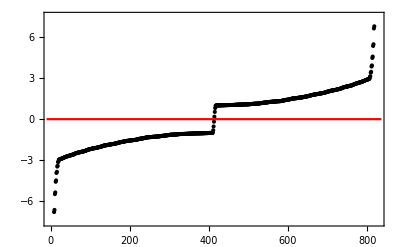

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black(**,PlotRange->{{0,84},{-2,2}}**)],Plot[0,{x,-10,NOrbitalsQuasi+10},PlotStyle-> Red]]
```

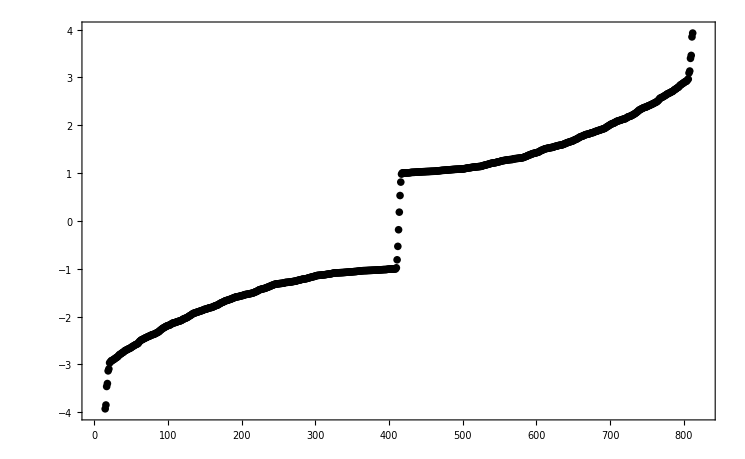

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}]]
```

```mathematica
(** This is for 48x48 **)
```

```mathematica
-Graphics-;
```

```mathematica
ValFibon
```

{{1,-63.4031},{2,-61.9774},{3,-21.0437},{4,-20.5689},{5,-12.5226},{6,-12.2387},{7,-8.843},{8,-8.6416},{9,-6.78548},{10,-6.63102},{11,-5.47402},{12,-5.35082},{13,-4.5733},{14,-4.47348},{15,-3.92867},{16,-3.84828},{17,-3.46146},{18,-3.39932},{19,-3.13506},{20,-3.09411},{21,-2.96592},{22,-2.95348},{23,-2.92558},{24,-2.92033},{25,-2.90969},{26,-2.90462},{27,-2.89333},{28,-2.87954},{29,-2.86774},{30,-2.86069},{31,-2.8481},{32,-2.83885},{33,-2.82086},{34,-2.80029},{35,-2.79103},{36,-2.781},{37,-2.77267},{38,-2.75634},{39,-2.75012},{40,-2.74042},{41,-2.72393},{42,-2.7103},{43,-2.70509},{44,-2.69884},{45,-2.68609},{46,-2.68244},{47,-2.67199},{48,-2.66468},{49,-2.6593},{50,-2.65065},{51,-2.63418},{52,-2.62954},{53,-2.61859},{54,-2.60558},{55,-2.59863},{56,-2.59159},{57,-2.58038},{58,-2.57512},{59,-2.56949},{60,-2.5562},{61,-2.52922},{62,-2.51591},{63,-2.50047},{64,-2.48743},{65,-2.48403},{66,-2.47423},{67,-2.46621},{68,-2.45704},{69,-2.45041},{70,-2.44223},{71,-2.43516},{72,-2.42835},{73,-2.41976},{74,-2.41152},{75,-2.40829},{76,-2.40191},{77,-2.39105},{78,-2.38391},{79,-2.37781},{80,-2.37557},{81,-2.37051},{82,-2.36386},{83,-2.35651},{84,-2.34609},{85,-2.34147},{86,-2.32929},{87,-2.32111},{88,-2.31675},{89,-2.29316},{90,-2.28735},{91,-2.2676},{92,-2.26204},{93,-2.24458},{94,-2.24114},{95,-2.2264},{96,-2.22227},{97,-2.20851},{98,-2.20533},{99,-2.1925},{100,-2.18925},{101,-2.18424},{102,-2.17865},{103,-2.17432},{104,-2.16407},{105,-2.15278},{106,-2.13968},{107,-2.13591},{108,-2.13117},{109,-2.12912},{110,-2.1241},{111,-2.11796},{112,-2.1117},{113,-2.10657},{114,-2.10154},{115,-2.09658},{116,-2.09206},{117,-2.08871},{118,-2.08095},{119,-2.07522},{120,-2.05989},{121,-2.05554},{122,-2.04347},{123,-2.0417},{124,-2.03448},{125,-2.02586},{126,-2.02149},{127,-2.01346},{128,-1.99731},{129,-1.9923},{130,-1.97778},{131,-1.97495},{132,-1.95933},{133,-1.95271},{134,-1.93624},{135,-1.93187},{136,-1.92797},{137,-1.9219},{138,-1.91515},{139,-1.91176},{140,-1.90639},{141,-1.89987},{142,-1.89416},{143,-1.89184},{144,-1.886},{145,-1.87634},{146,-1.87519},{147,-1.87005},{148,-1.86509},{149,-1.8526},{150,-1.8489},{151,-1.84595},{152,-1.84273},{153,-1.83844},{154,-1.83137},{155,-1.82463},{156,-1.81853},{157,-1.81669},{158,-1.813},{159,-1.80897},{160,-1.80625},{161,-1.79802},{162,-1.79429},{163,-1.78337},{164,-1.77603},{165,-1.77112},{166,-1.76682},{167,-1.76048},{168,-1.75635},{169,-1.74288},{170,-1.73365},{171,-1.72657},{172,-1.71413},{173,-1.70801},{174,-1.70312},{175,-1.69759},{176,-1.68652},{177,-1.6798},{178,-1.6705},{179,-1.66565},{180,-1.66313},{181,-1.65775},{182,-1.65254},{183,-1.64559},{184,-1.64159},{185,-1.63818},{186,-1.63061},{187,-1.62553},{188,-1.61493},{189,-1.61092},{190,-1.60607},{191,-1.59728},{192,-1.59124},{193,-1.58875},{194,-1.58529},{195,-1.58316},{196,-1.58144},{197,-1.5767},{198,-1.57371},{199,-1.5674},{200,-1.56269},{201,-1.56067},{202,-1.55766},{203,-1.55148},{204,-1.5448},{205,-1.53901},{206,-1.53671},{207,-1.53543},{208,-1.53185},{209,-1.52945},{210,-1.5248},{211,-1.52193},{212,-1.51875},{213,-1.51739},{214,-1.51073},{215,-1.50844},{216,-1.50431},{217,-1.49636},{218,-1.48952},{219,-1.48009},{220,-1.47511},{221,-1.47398},{222,-1.45749},{223,-1.45104},{224,-1.43943},{225,-1.43557},{226,-1.43268},{227,-1.42606},{228,-1.42368},{229,-1.41812},{230,-1.41506},{231,-1.41181},{232,-1.40789},{233,-1.40219},{234,-1.39217},{235,-1.38907},{236,-1.38574},{237,-1.37263},{238,-1.36995},{239,-1.36686},{240,-1.35371},{241,-1.35024},{242,-1.34153},{243,-1.34053},{244,-1.33118},{245,-1.32344},{246,-1.32152},{247,-1.31936},{248,-1.31644},{249,-1.31532},{250,-1.3131},{251,-1.31043},{252,-1.30866},{253,-1.30758},{254,-1.30578},{255,-1.30339},{256,-1.30228},{257,-1.30135},{258,-1.29488},{259,-1.28779},{260,-1.28602},{261,-1.28501},{262,-1.28402},{263,-1.282},{264,-1.28077},{265,-1.27907},{266,-1.27754},{267,-1.27397},{268,-1.2711},{269,-1.26935},{270,-1.26631},{271,-1.26335},{272,-1.26114},{273,-1.25905},{274,-1.25702},{275,-1.25006},{276,-1.24417},{277,-1.2408},{278,-1.23724},{279,-1.23525},{280,-1.23004},{281,-1.22583},{282,-1.22122},{283,-1.2177},{284,-1.21541},{285,-1.2146},{286,-1.2097},{287,-1.20875},{288,-1.20642},{289,-1.19992},{290,-1.19801},{291,-1.19087},{292,-1.18605},{293,-1.18258},{294,-1.179},{295,-1.1731},{296,-1.1705},{297,-1.16561},{298,-1.16153},{299,-1.1601},{300,-1.15254},{301,-1.14646},{302,-1.14222},{303,-1.13953},{304,-1.13847},{305,-1.13724},{306,-1.13527},{307,-1.13347},{308,-1.13229},{309,-1.1314},{310,-1.1287},{311,-1.12736},{312,-1.12524},{313,-1.12364},{314,-1.12151},{315,-1.11908},{316,-1.11508},{317,-1.11425},{318,-1.11132},{319,-1.10942},{320,-1.10728},{321,-1.10459},{322,-1.10277},{323,-1.09661},{324,-1.09436},{325,-1.09335},{326,-1.08712},{327,-1.08632},{328,-1.08559},{329,-1.08521},{330,-1.08472},{331,-1.08411},{332,-1.08367},{333,-1.08221},{334,-1.08181},{335,-1.08055},{336,-1.07999},{337,-1.0795},{338,-1.07846},{339,-1.07629},{340,-1.07619},{341,-1.07542},{342,-1.07289},{343,-1.07222},{344,-1.07093},{345,-1.06918},{346,-1.06793},{347,-1.06698},{348,-1.06509},{349,-1.06386},{350,-1.0629},{351,-1.06244},{352,-1.05969},{353,-1.05884},{354,-1.05818},{355,-1.0568},{356,-1.05588},{357,-1.05298},{358,-1.05123},{359,-1.05002},{360,-1.04871},{361,-1.04619},{362,-1.04449},{363,-1.04382},{364,-1.04049},{365,-1.03959},{366,-1.03911},{367,-1.03875},{368,-1.03804},{369,-1.03756},{370,-1.03722},{371,-1.03617},{372,-1.03523},{373,-1.03442},{374,-1.03423},{375,-1.03349},{376,-1.0331},{377,-1.03197},{378,-1.03135},{379,-1.03049},{380,-1.03008},{381,-1.02929},{382,-1.02853},{383,-1.02816},{384,-1.02645},{385,-1.02584},{386,-1.02432},{387,-1.02308},{388,-1.02218},{389,-1.02165},{390,-1.0202},{391,-1.01928},{392,-1.01785},{393,-1.01706},{394,-1.01673},{395,-1.01596},{396,-1.01554},{397,-1.01425},{398,-1.0112},{399,-1.00897},{400,-1.00692},{401,-1.00589},{402,-1.00545},{403,-1.00529},{404,-1.00495},{405,-1.00479},{406,-1.00436},{407,-1.00423},{408,-1.004},{409,-1.00384},{410,-0.979118},{411,-0.812215},{412,-0.531373},{413,-0.183933},{414,0.183933},{415,0.531373},{416,0.812215},{417,0.979118},{418,1.00384},{419,1.004},{420,1.00423},{421,1.00436},{422,1.00479},{423,1.00495},{424,1.00529},{425,1.00545},{426,1.00589},{427,1.00692},{428,1.00897},{429,1.0112},{430,1.01425},{431,1.01554},{432,1.01596},{433,1.01673},{434,1.01706},{435,1.01785},{436,1.01928},{437,1.0202},{438,1.02165},{439,1.02218},{440,1.02308},{441,1.02432},{442,1.02584},{443,1.02645},{444,1.02816},{445,1.02853},{446,1.02929},{447,1.03008},{448,1.03049},{449,1.03135},{450,1.03197},{451,1.0331},{452,1.03349},{453,1.03423},{454,1.03442},{455,1.03523},{456,1.03617},{457,1.03722},{458,1.03756},{459,1.03804},{460,1.03875},{461,1.03911},{462,1.03959},{463,1.04049},{464,1.04382},{465,1.04449},{466,1.04619},{467,1.04871},{468,1.05002},{469,1.05123},{470,1.05298},{471,1.05588},{472,1.0568},{473,1.05818},{474,1.05884},{475,1.05969},{476,1.06244},{477,1.0629},{478,1.06386},{479,1.06509},{480,1.06698},{481,1.06793},{482,1.06918},{483,1.07093},{484,1.07222},{485,1.07289},{486,1.07542},{487,1.07619},{488,1.07629},{489,1.07846},{490,1.0795},{491,1.07999},{492,1.08055},{493,1.08181},{494,1.08221},{495,1.08367},{496,1.08411},{497,1.08472},{498,1.08521},{499,1.08559},{500,1.08632},{501,1.08712},{502,1.09335},{503,1.09436},{504,1.09661},{505,1.10277},{506,1.10459},{507,1.10728},{508,1.10942},{509,1.11132},{510,1.11425},{511,1.11508},{512,1.11908},{513,1.12151},{514,1.12364},{515,1.12524},{516,1.12736},{517,1.1287},{518,1.1314},{519,1.13229},{520,1.13347},{521,1.13527},{522,1.13724},{523,1.13847},{524,1.13953},{525,1.14222},{526,1.14646},{527,1.15254},{528,1.1601},{529,1.16153},{530,1.16561},{531,1.1705},{532,1.1731},{533,1.179},{534,1.18258},{535,1.18605},{536,1.19087},{537,1.19801},{538,1.19992},{539,1.20642},{540,1.20875},{541,1.2097},{542,1.2146},{543,1.21541},{544,1.2177},{545,1.22122},{546,1.22583},{547,1.23004},{548,1.23525},{549,1.23724},{550,1.2408},{551,1.24417},{552,1.25006},{553,1.25702},{554,1.25905},{555,1.26114},{556,1.26335},{557,1.26631},{558,1.26935},{559,1.2711},{560,1.27397},{561,1.27754},{562,1.27907},{563,1.28077},{564,1.282},{565,1.28402},{566,1.28501},{567,1.28602},{568,1.28779},{569,1.29488},{570,1.30135},{571,1.30228},{572,1.30339},{573,1.30578},{574,1.30758},{575,1.30866},{576,1.31043},{577,1.3131},{578,1.31532},{579,1.31644},{580,1.31936},{581,1.32152},{582,1.32344},{583,1.33118},{584,1.34053},{585,1.34153},{586,1.35024},{587,1.35371},{588,1.36686},{589,1.36995},{590,1.37263},{591,1.38574},{592,1.38907},{593,1.39217},{594,1.40219},{595,1.40789},{596,1.41181},{597,1.41506},{598,1.41812},{599,1.42368},{600,1.42606},{601,1.43268},{602,1.43557},{603,1.43943},{604,1.45104},{605,1.45749},{606,1.47398},{607,1.47511},{608,1.48009},{609,1.48952},{610,1.49636},{611,1.50431},{612,1.50844},{613,1.51073},{614,1.51739},{615,1.51875},{616,1.52193},{617,1.5248},{618,1.52945},{619,1.53185},{620,1.53543},{621,1.53671},{622,1.53901},{623,1.5448},{624,1.55148},{625,1.55766},{626,1.56067},{627,1.56269},{628,1.5674},{629,1.57371},{630,1.5767},{631,1.58144},{632,1.58316},{633,1.58529},{634,1.58875},{635,1.59124},{636,1.59728},{637,1.60607},{638,1.61092},{639,1.61493},{640,1.62553},{641,1.63061},{642,1.63818},{643,1.64159},{644,1.64559},{645,1.65254},{646,1.65775},{647,1.66313},{648,1.66565},{649,1.6705},{650,1.6798},{651,1.68652},{652,1.69759},{653,1.70312},{654,1.70801},{655,1.71413},{656,1.72657},{657,1.73365},{658,1.74288},{659,1.75635},{660,1.76048},{661,1.76682},{662,1.77112},{663,1.77603},{664,1.78337},{665,1.79429},{666,1.79802},{667,1.80625},{668,1.80897},{669,1.813},{670,1.81669},{671,1.81853},{672,1.82463},{673,1.83137},{674,1.83844},{675,1.84273},{676,1.84595},{677,1.8489},{678,1.8526},{679,1.86509},{680,1.87005},{681,1.87519},{682,1.87634},{683,1.886},{684,1.89184},{685,1.89416},{686,1.89987},{687,1.90639},{688,1.91176},{689,1.91515},{690,1.9219},{691,1.92797},{692,1.93187},{693,1.93624},{694,1.95271},{695,1.95933},{696,1.97495},{697,1.97778},{698,1.9923},{699,1.99731},{700,2.01346},{701,2.02149},{702,2.02586},{703,2.03448},{704,2.0417},{705,2.04347},{706,2.05554},{707,2.05989},{708,2.07522},{709,2.08095},{710,2.08871},{711,2.09206},{712,2.09658},{713,2.10154},{714,2.10657},{715,2.1117},{716,2.11796},{717,2.1241},{718,2.12912},{719,2.13117},{720,2.13591},{721,2.13968},{722,2.15278},{723,2.16407},{724,2.17432},{725,2.17865},{726,2.18424},{727,2.18925},{728,2.1925},{729,2.20533},{730,2.20851},{731,2.22227},{732,2.2264},{733,2.24114},{734,2.24458},{735,2.26204},{736,2.2676},{737,2.28735},{738,2.29316},{739,2.31675},{740,2.32111},{741,2.32929},{742,2.34147},{743,2.34609},{744,2.35651},{745,2.36386},{746,2.37051},{747,2.37557},{748,2.37781},{749,2.38391},{750,2.39105},{751,2.40191},{752,2.40829},{753,2.41152},{754,2.41976},{755,2.42835},{756,2.43516},{757,2.44223},{758,2.45041},{759,2.45704},{760,2.46621},{761,2.47423},{762,2.48403},{763,2.48743},{764,2.50047},{765,2.51591},{766,2.52922},{767,2.5562},{768,2.56949},{769,2.57512},{770,2.58038},{771,2.59159},{772,2.59863},{773,2.60558},{774,2.61859},{775,2.62954},{776,2.63418},{777,2.65065},{778,2.6593},{779,2.66468},{780,2.67199},{781,2.68244},{782,2.68609},{783,2.69884},{784,2.70509},{785,2.7103},{786,2.72393},{787,2.74042},{788,2.75012},{789,2.75634},{790,2.77267},{791,2.781},{792,2.79103},{793,2.80029},{794,2.82086},{795,2.83885},{796,2.8481},{797,2.86069},{798,2.86774},{799,2.87954},{800,2.89333},{801,2.90462},{802,2.90969},{803,2.92033},{804,2.92558},{805,2.95348},{806,2.96592},{807,3.09411},{808,3.13506},{809,3.39932},{810,3.46146},{811,3.84828},{812,3.92867},{813,4.47348},{814,4.5733},{815,5.35082},{816,5.47402},{817,6.63102},{818,6.78548},{819,8.6416},{820,8.843},{821,12.2387},{822,12.5226},{823,20.5689},{824,21.0437},{825,61.9774},{826,63.4031}}

```mathematica
(** Export["m=-3QuasiEnergiesPerfectLatticePBC.dat",ValFibon]; **)
```

```mathematica
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,NOrbitalsQuasi}];
```

```mathematica
Tr[OnlyEigenvalue]//Chop
```

0

```mathematica
(**---- Calculation of Bott Index of the quasicrystal ----**)
```

```mathematica
(** FilledEigenvectors=Table[ValVecFibon[[i]][[2]], {i,1,NOrbitalsQuasi/2}]; **)
```

```mathematica
(** We create a projector P on the space of filled eigenstates **)
```

```mathematica
(** P = Table[0,{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}]; **)
```

```mathematica
(** Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i, 1, NOrbitalsQuasi/2}]; **)
```

```mathematica
(** Dimensions[P] **)
```

```mathematica
(** U = P . Ux . P + IdentityMatrix[NOrbitalsQuasi] - P; **)
```

```mathematica
(** V = P . Vy . P + IdentityMatrix[NOrbitalsQuasi] - P; **)
```

```mathematica
(** To save computer from hanging, we clear some memory **)
```

```mathematica
(** Clear[ Bott, LogEigenValuesBott, BottIndexQuasi] **)
```

```mathematica
(** Bott = U.V.ConjugateTranspose[U].ConjugateTranspose[V]; **)
```

```mathematica
(** Clear[P,U,V, Ux, Vy] **)
```

```mathematica
(** LogEigenValuesBott=Log[Eigenvalues[Bott]]; **)
```

Bott index of quasicrystal

```mathematica
(** BottIndexQuasi = Re[(I/(2π))Total[LogEigenValuesBott]] **)
```

```mathematica
(** percentageOfOrbitalsInside = N[NOrbitalsQuasi/(2*A)] **)
```

```mathematica
(** NSitesInside = NOrbitalsQuasi/2 **)
```

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi/2}];
Dimensions[Fibon1D]
```

{414,2}

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

301

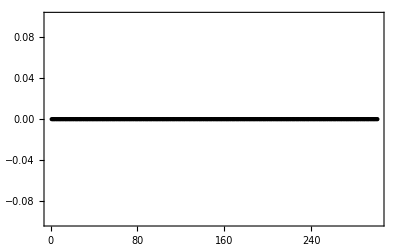

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black,PlotStyle->Small]
```

```mathematica
Fibon1D[[3,1]]
```

2.37638

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ValFibon[[(NOrbitalsQuasi/2)+1,2]]
```

0.183933

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabDataFibon=Table[{Fibon1D[[i,1]],0,
Abs[ValVecFibon[[J,2,2i]]]^2+Abs[ValVecFibon[[J,2,2i-1]]]^2

+Abs[ValVecFibon[[J+1,2,2i]]]^2+Abs[ValVecFibon[[J+1,2,2i-1]]]^2

},{i,1,NOrbitalsQuasi/2}];
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
(** Divide the last term by 2 for normalization **)
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]/2},{i,1,3*NOrbitalsQuasi/2,3}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,rng,P1]
```

```mathematica
(** Colorful **)
```

```mathematica
(**colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]]; **)
```

```mathematica
(** Mono color **)
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.2*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
(** Black and White **)
```

```mathematica
(** colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]];**)
```

```mathematica
rngOld={0,Max[#]}&@(TabFibonacci[[All,3]])
```

{0,0.0589715}

```mathematica
rng = {0,0.2}
```

{0,0.2}

```mathematica
rng[[2]]
```

0.2

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"1x10^-2"},{rng[[2]]-10^-3,"2x10^-2"}}]
```

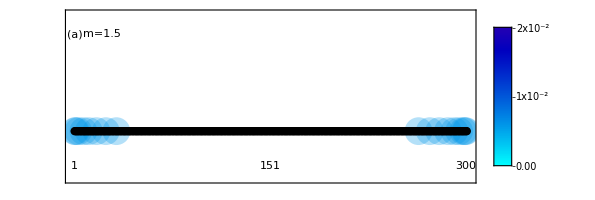

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameTicks-> {None,None},FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX+1},{-3.5,8.5}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}]
,
Epilog-> {Inset[1,{1,-2.5}],Inset[Ceiling[largestX/2],{Ceiling[largestX/2],-2.5}],Inset[largestX-1,{largestX-1,-2.5}],
Rotate[Inset[P1,{10.5,5.00}],90 Degree],Inset["m=1.5",{21.5,7}],
Inset["(a)",{1.25,7}]
}
]
```

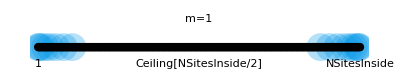

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
BaseStyle-> 18,
PlotRange-> {{-0.5,largestX+2},{-4.5,7}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}],
Epilog-> {Inset[1,{1,-3}],Inset[Ceiling[NSitesInside/2],{Ceiling[largestX/2],-3}],Inset[NSitesInside,{largestX,-3}],Inset["m=1",{largestX/2,5}]
}
]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ArrayPlot[Re[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
ArrayPlot[Im[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ArrayPlot[Re[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
ArrayPlot[Im[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

-Graphics-